```mathematica
Eff=Import[NotebookDirectory[]<>"../calc/efficencies.txt","Table"];
Eff//MatrixForm
EffErr=Import[NotebookDirectory[]<>"../calc/efficencies_error.txt","Table"];
EffErr//MatrixForm
```

(0.391474 | 0.000011 | 0.004406 | 0.00001
0.00016 | 0.890762 | 0.003585 | 0.
0.01259 | 0.031002 | 0.848524 | 0.000457
0. | 0. | 0.001868 | 0.966965)

(0.001594 | 0.000011 | 0.000235 | 0.00001
0.000041 | 0.001015 | 0.000212 | 0.
0.000364 | 0.000564 | 0.001274 | 0.000068
0. | 0. | 0.000153 | 0.000569)

{1.16113,0.412444,0.375917,1.50868,1.99971}

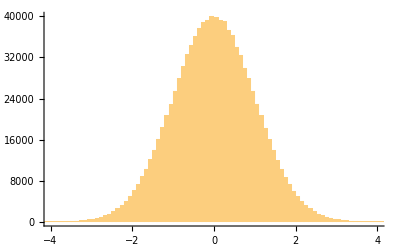

```mathematica
rns=RandomVariate[NormalDistribution[],1000000];
rns[[1;;5]]
Histogram[rns,100,PlotRange->{{-4,4},All}]
```

```mathematica
NoisyInvEff=Inverse[Eff+EffErr*#]&/@rns;
```

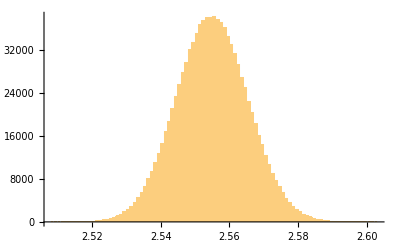

```mathematica
Histogram[NoisyInvEff[[All,1,1]],100,PlotRange->{All,All}]
```

```mathematica
NoisyInvEffSort=Table[NoisyInvEff[[All,i,j]],{i,1,4},{j,1,4}];
Inverse[Eff]
A=Mean[#]&/@#&/@NoisyInvEffSort;
A//MatrixForm
EffErr//MatrixForm
sA=StandardDeviation[#]&/@#&/@NoisyInvEffSort;
sA//MatrixForm
```

{{2.55487,0.000430231,-0.0132681,-0.0000201509},{-0.000306389,1.1228,-0.00474222,2.2444×10^-6},{-0.0378969,-0.0410295,1.17889,-0.000556766},{0.0000732098,0.0000792614,-0.0022774,1.03416}}

(2.55493 | 0.000430637 | -0.0132639 | -0.0000199651
-0.000305526 | 1.1228 | -0.00474126 | 2.26324×10^-6
-0.0378909 | -0.0410272 | 1.17889 | -0.000556518
0.0000733282 | 0.000079348 | -0.00227687 | 1.03417)

(0.001594 | 0.000011 | 0.000235 | 0.00001
0.000041 | 0.001015 | 0.000212 | 0.
0.000364 | 0.000564 | 0.001274 | 0.000068
0. | 0. | 0.000153 | 0.000569)

(0.0103674 | 1.56588×10^-6 | 0.0006337 | 0.0000250646
0.0001028 | 0.00126666 | 0.000267351 | 4.63241×10^-7
0.000881068 | 0.000638379 | 0.00174115 | 0.0000813249
7.65271×10^-6 | 7.6766×10^-6 | 0.000181768 | 0.000608091)

```mathematica
Threshold[Eff.A,10^-6]//MatrixForm
```

(1.00002 | 0. | 1.64238×10^-6 | 0.
0. | 1. | 0. | 0.
5.70601×10^-6 | 2.02434×10^-6 | 1. | 0.
0. | 0. | 0. | 1.)

```mathematica
Export[NotebookDirectory[]<>"../calc/invEfficencies_Math.txt",A,"Table"];
Export[NotebookDirectory[]<>"../calc/invEfficencies_error_Math.txt",sA,"Table"];
```